```mathematica
(*N is the number of travelers; 
c is the cost; 
tc is the total cost;
d is the cost parameter, d=beta*gamma/(beta+gamma);
dr is dl/dh=beta^l/beta^h;
m is (beta^l/alpha^l)/(beta^h/alpha^h). 0<m<1;
h means the group with high beta/alpha, thus who travels in the center;
Group costs are decided by betah/betal (how important to arrive on time) and m(how impatient to wait in line);
i is the group, i=h(high),l(low);
j is the period, j=t(tradable credit),nt(no tradible credit);
c is the congestion cost;*)
Clear[Nht,Nhnt,Nlt,Nlnt,cht,clt,chnt,clnt,dl,dh,dr,m,Nh,Nl,tc]
(*control variables: Nhnt,Nlnt*)
Nht=Nh-Nhnt ;
Nlt=Nl-Nlnt;
dh=1;
dl=dr*dh;
cht=dh*(Nht+Nlt*m);
clt=dl*(Nht+Nlt);
chnt=dh*(Nht+Nlt+Nhnt+Nlnt*m);
clnt=dl*(Nht+Nlt+Nhnt+Nlnt);
tc=cht*Nht+clt*Nlt+chnt*Nhnt+clnt*Nlnt
```

(Nh-Nhnt) (Nh-Nhnt+m (Nl-Nlnt))+dr (Nl-Nlnt) (Nh-Nhnt+Nl-Nlnt)+dr (Nh+Nl) Nlnt+Nhnt (Nh+Nl-Nlnt+m Nlnt)

```mathematica
(*foc*)
Simplify[Solve[D[tc,{{Nhnt,Nlnt},1}]=={0,0},{Nhnt,Nlnt}]]
(*hessian*)
MatrixForm[D[tc,{{Nhnt,Nlnt},2}]]
Simplify[2 *2 dr-(-1+dr+2 m)^2]
```

{{Nhnt→(m (-1+2 m) Nh-dr^2 Nl+dr ((-2+m) Nh+Nl))/(dr^2+(1-2 m)^2+dr (-6+4 m)),Nlnt→((-1+dr) Nh+(1+dr^2-3 m+2 m^2+dr (-4+3 m)) Nl)/(dr^2+(1-2 m)^2+dr (-6+4 m))}}

(2 | -1+dr+2 m
-1+dr+2 m | 2 dr)

4 dr-(-1+dr+2 m)^2

4-4 m^2

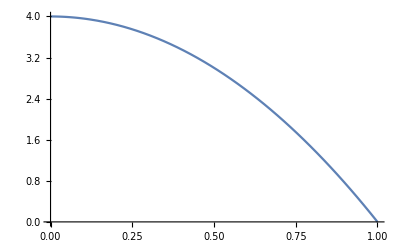

{{Nhnt→Nh/2,Nlnt→Nl/2}}

case I: beta and gamma are fixed, only alpha varies, i.e. dr=1. hessian is positive definite, means always an interior solution. Both types travel on both periods.

```mathematica
(*Case I: if beta^h=beta^l and gamma^h=gamma^l, so only alpha changes.*)
(*hessian*)Simplify[4 dr-(-1+dr +2  m)^2]/.{dr->1}
Plot[4 dr-(-1+dr +2 m)^2/.{dr->1}, {m,0,1}]
Simplify[Solve[D[tc,{{Nhnt,Nlnt},1}]=={0,0},{Nhnt,Nlnt}]/.{dr->1}]
Print["case I: beta and gamma are fixed, only alpha varies, i.e. dr=1. hessian is positive definite, means always an interior solution. Both types travel on both periods."]
```

4 m-(-1+3 m)^2

{{m→1/9},{m→1}}

{{Nhnt→(m (3 Nh-Nl))/(-1+9 m),Nlnt→(Nh+(-1+6 m) Nl)/(-1+9 m)}}

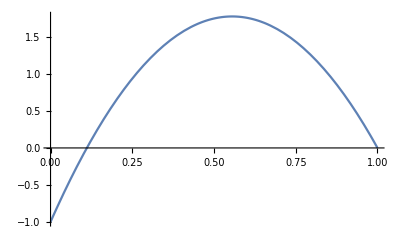

case II: alpha is fixed, only beta and gamma vary, i.e. dr=m. hessian is positive definite if m>1/9 and indefinite if m<1/9.

```mathematica
(*Case II: if alpha^h=alpha^l, only beta and gamma vary, so dr=m.*)
4 dr-(-1+dr +2 m)^2/.{dr->m}
Solve[4 m-(-1+3 m)^2==0,{m}]
Simplify[Solve[D[tc,{{Nhnt,Nlnt},1}]=={0,0},{Nhnt,Nlnt}]/.{dr->m}]
Plot[4 dr-(-1+dr +2*m)^2/.{dr->m},{m,0,1}]
Print["case II: alpha is fixed, only beta and gamma vary, i.e. dr=m. hessian is positive definite if m>1/9 and indefinite if m<1/9."]
```

```mathematica
(*Check when 0<Nhnt=(m (3 Nh-Nl))/(-1+9 m)<Nh and 0<Nlnt=(Nh+(-1+6 m) Nl)/(-1+9 m)<Nl*)
Simplify[{(m (3 Nh-Nl))/(-1+9 m)-0,(Nh+(-1+6 m) Nl)/(-1+9 m)-0}](*both shoud >0*)
Print["Given m>1/9, when Nh>1/3Nl, both >0."]
Simplify[{(m (3 Nh-Nl))/(-1+9 m)-Nh,(Nh+(-1+6 m) Nl)/(-1+9 m)-Nl}](*both should <0*)
Print["Given m>1/9, For Nlnt<Nl, when Nh<3mNl(>1/3Nl), good. For Nhnt<Nh, when 1/9<m<1/6, Nh<m/(1-6m)Nl, good; if m>1/6, whatever Nh is fine. Since 3m<m/(1-6m)for 1/9<m<1/6. So in sum, when Nh<3mNl, then Nhnt<Nh and Nlnt<Nl."]
```

{(m (3 Nh-Nl))/(-1+9 m),(Nh+(-1+6 m) Nl)/(-1+9 m)}

Given m>1/9, when Nh>1/3Nl, both >0.

{(Nh-6 m Nh-m Nl)/(-1+9 m),(Nh-3 m Nl)/(-1+9 m)}

Given m>1/9, For Nlnt<Nl, when Nh<3mNl(>1/3Nl), good. For Nhnt<Nh, when 1/9<m<1/6, Nh<m/(1-6m)Nl, good; if m>1/6, whatever Nh is fine. Since 3m<m/(1-6m)for 1/9<m<1/6. So in sum, when Nh<3mNl, then Nhnt<Nh and Nlnt<Nl.

```mathematica
(*for example*)
{(m (3 Nh-Nl))/(-1+9 m)-0,(Nh+(-1+6 m) Nl)/(-1+9 m)-0,(m (3 Nh-Nl))/(-1+9 m)-Nh,(Nh+(-1+6 m) Nl)/(-1+9 m)-Nl}/.{m->1/2,Nl->1,Nh-> 2/3}
```

{1/7,16/21,-11/21,-5/21}

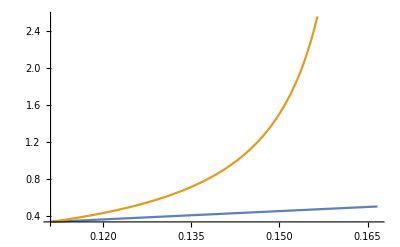

```mathematica
Manipulate[Plot[{(m-3 m Nh)/(1-9 m),0,Nh},{m,1/9+0.000001,1}],{Nh,0,3}]
Manipulate[Plot[{(-1+6 m+Nh)/(-1+9 m),0,1},{m,1/9+0.000001,1}],{Nh,0,3}]
Plot[{3*m, m/(1-6*m)},{m,1/9+0.000001,1/6-0.000001}]
```

{{dr→3-2 √2 √(1-m)-2 m},{dr→3+2 √2 √(1-m)-2 m}}

{{Nhnt→(m (-1+2 m) Nh-dr^2 Nl+dr ((-2+m) Nh+Nl))/(dr^2+(1-2 m)^2+dr (-6+4 m)),Nlnt→((-1+dr) Nh+(1+dr^2-3 m+2 m^2+dr (-4+3 m)) Nl)/(dr^2+(1-2 m)^2+dr (-6+4 m))}}

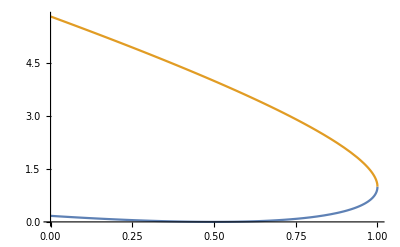

```mathematica
(*Case III: general case, alpha, beta and gamma all vary.*)
Solve[4 dr-(-1+dr +2 m)^2==0,{dr}]
Simplify[Solve[D[tc,{{Nhnt,Nlnt},1}]=={0,0},{Nhnt,Nlnt}]]
Plot[{3-2 √2 √(1-m)-2 m,3+2 √2 √(1-m)-2 m},{m,0,1}]
Solve[dr^2+(1-2 m)^2+dr (-6+4 m)==0,{dr}]
Print["As m increases, the range of dr that makes Hessian positive definite is decreasing. But anyway dr=1 is included. "]
```

```mathematica
{{dr->3-2 √2 √(1-m)-2 m},{dr->3+2 √2 √(1-m)-2 m}}
```

{{dr→3-2 √2 √(1-m)-2 m},{dr→3+2 √2 √(1-m)-2 m}}

```mathematica
Simplify[{(m (-1+2 m) Nh-dr^2 Nl+dr ((-2+m) Nh+Nl))/(dr^2+(1-2 m)^2+dr (-6+4 m))-Nh,((-1+dr) Nh+(1+dr^2-3 m+2 m^2+dr (-4+3 m)) Nl)/(dr^2+(1-2 m)^2+dr (-6+4 m))-Nl}]
```

{-Nh+(m (-1+2 m) Nh-dr^2 Nl+dr ((-2+m) Nh+Nl))/(dr^2+(1-2 m)^2+dr (-6+4 m)),((-1+dr) Nh+(-dr (-2+m)+m-2 m^2) Nl)/(dr^2+(1-2 m)^2+dr (-6+4 m))}